Harlan Brawer, 704924872, harlanbrawer@gmail.com, 105B hw2

```mathematica
(* 1 *)
Remove["Global`*"]
mat = {{m1 g L + k L - m1 L^2 ω^2, -k L},
{-k L,m2 g L + k L - m2 L^2 ω^2}};
char=Det[mat] ==0;
sol=Solve[char,ω];
ω1=ω/.sol[[2]]
ω2=ω/.sol[[4]]
```

(√g)/(√L)

(√(k m1+k m2+g m1 m2))/(√L √m1 √m2)

```mathematica
(*2 *)
Remove["Global`*"]

SetAttributes[{m1,m2,g,k,L},Constant];
$Assumptions={Element[clist,Reals]};

T =1/2 m1 x1'[t]^2+1/2 m2 ( (x1'[t]+L*Cos[θ[t]]θ'[t])^2 + (-L*Sin[θ[t]]θ'[t])^2);
U =-m2 g L Cos[θ] + 1/2 k x1[t]^2;

lag = T-U;
EE = T+U;

EL[q_]:= D[lag,q] - Dt[ D[lag,D[q,t]], t]==0//Simplify;
xeq=EL[x1[t]];
θeq=EL[θ[t]];
smalleqs={xeq,θeq}/.{Sin[θ[t]]->θ[t],Cos[θ[t]]->1};
eqs=smalleqs/.{x1[t]->A,θ[t]->B ,x1'[t]->I ω A,θ'[t]->I ω B, x1''[t]->-ω^2* A,θ''[t]->-ω^2*B};


mat = {{k-(m1+m2)^2, - L m2 ω^2},
{-L m2 ω^2,-L^2 m2 ω^2}};
char=Det[mat] ==0;
sol=Solve[char,ω];
Print["Eigenfrequecies, one is zero"]
ω1=ω/.sol[[2]]
ω2=ω/.sol[[4]]
```

Eigenfrequecies, one is zero

0

(√(-k+m1^2+2 m1 m2+m2^2))/(√m2)

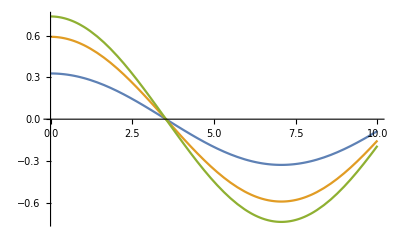

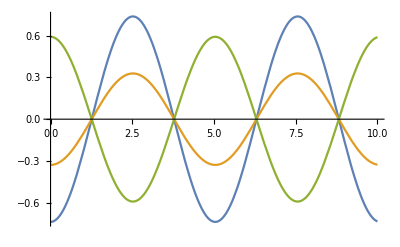

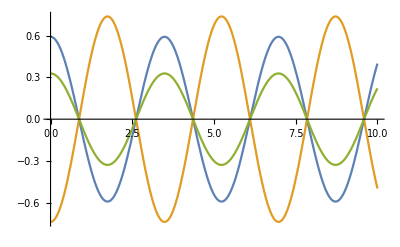

```mathematica
(* 3 *)
Remove["Global`*"]
SetAttributes[{m1,m2,m3,k1,k2,k3},Constant];
$Assumptions={Element[{m1,m2,m3,k1,k2,k3},Reals]&&m1>0&&m2>0&&m3≥0&&k1>0&&k2>0&&k3>0};
pos[t_]={x1[t],x2[t],x3[t]};
vel[t_]=D[pos[t],t];
T=1/2 m1 (x1'[t])^2+1/2 m1 (x2'[t])^2+1/2 m3 (x3'[t])^2;
U=1/2 k1(x1[t])^2+1/2 k2(x2[t]-x1[t])^2+1/2 k3(x3[t]-x2[t])^2;
Lag=T-U;

m1=1.0;m2=1.0;m3=1.0;k1=1.0;k2=1.0;k3=1.0;

A=Table[D[U,pos[t][[i]],pos[t][[j]]],{i,1,3},{j,1,3}];
M=Table[D[T,vel[t][[i]],vel[t][[j]]],{i,1,3},{j,1,3}];
solLamb=Solve[Det[A-λ M]==0,λ];
mode=Table[Normalize[NullSpace[(A-λ M)/.solLamb[[i]]][[1]]],{i,1,3}];

EL[q_]:=D[Lag,q]-D[D[Lag,D[q,t]],t]==0;
eqns=Table[EL[pos[t][[i]]],{i,1,3}];
icList[i_]={pos[0]==mode[[i]],vel[0]=={0,0,0}};

sol[i_]:=NDSolve[Join[eqns,icList[i]],pos[t],{t,0,10}];

EigenPlot[i_]:=Plot[Evaluate[pos[t]/.sol[i]],{t,0,10}];
EigenPlot[1]
EigenPlot[2]
EigenPlot[3]
```